```mathematica
Clear[LinearSumInterpolation];
LinearSumInterpolation[list_]:=Interpolation[{{0, 0}, {1, 0}, {2, 1}, {3, 0}, {4, 1}, {5, 0}}, InterpolationOrder->1][Total[list]]
NonlinearSumInterpolation[list_]:=With[{o=LinearSumInterpolation[list]}, 0.6o+0.4o^2]
```

```mathematica
StepCode20Interped[interp_][list_]:=interp/@Partition[ArrayPad[list,2],5,1]
StepCode20InterpedPar[interp_][list_]:=ParallelMap[interp,Partition[ArrayPad[list,2],5,1]]
RunCode20Interped[interp_][list_, steps_]:=NestList[StepCode20Interped[interp], list, steps]
RunCode20InterpedPar[interp_][list_, steps_]:=NestList[StepCode20InterpedPar[interp], list, steps]
```

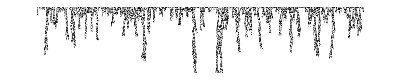

```mathematica
ArrayPlot[RunCode20InterpedPar[NonlinearSumInterpolation][RandomReal[{0, 1}, 1000], 100]]
```

```mathematica
ArrayPlot[Transpose[RunCode20Interped[LinearSumInterpolation][RandomReal[{0, 1}, 100], 10000]], ImageSize->{Automatic, 300}]
```

-Graphics-

```mathematica
frames={};
o=ConstantArray[0, {20, 20}];
o[[1]]=CenterArray[RandomReal[{0, 1},10], Length[First[o]]];
first=o[[1]];
counter=0;
Do[
AppendTo[frames, NumericArray[o, "Real32"]];
new=ParallelTable[StepCode20Interped[LinearSumInterpolation][o[[If[i==1, Length[o],i-1]]]], {i, Length[o]}];
o=(o+new)/2;
If[Max[o[[-1]]]<0.01&&counter<6,o[[1]]=first; counter++]; 

,1000
]
```

```mathematica
Animate[ArrayPlot[Normal[ff]], {ff, frames}, AnimationRate->30]
```

```mathematica
Do[
AppendTo[frames, NumericArray[o, "Real32"]];
new=ParallelTable[StepCode20Interped[LinearSumInterpolation][o[[If[i==1, Length[o],i-1]]]], {i, Length[o]}];
o=(o+new)/2;

, 1000
]
```

```mathematica
Clear[LossPeriodic]
LossPeriodic[interp_, p_][list_]:=With[
{carun=RunCode20Interped[interp][list, p]},
Norm[Last[carun]-list]-Max[list]-0.1Sum[Norm[carun[[i+1]]-list], {i,Complement[Divisors[p], {p}]}]
]

LossPeriodic[LinearSumInterpolation, 2][{1, 0, 1, 1, 1, 1, 0, 1}]
LossPeriodic[LinearSumInterpolation, 2][{1,0,0,1,0,1,1,1, 0}]
```

-1.

-1.24495

```mathematica
GrayCode=ResourceFunction["GrayCode"];
GrayCodeList[l_List]:=With[{gc=GrayCode[l]}, {maxlen=Max[Length/@gc]},PadLeft[#, maxlen]&/@gc]
```

```mathematica
numBits=10;
gci=Interpolation[Transpose[{Range[0, 2^numBits-1], GrayCodeList[Range[0, 2^numBits-1]]}], InterpolationOrder->1];
```

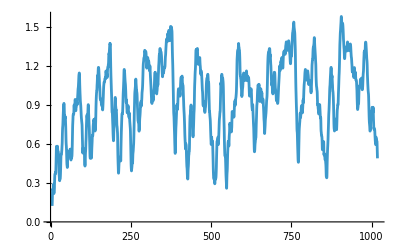

```mathematica
ListLinePlot[MovingAverage[ParallelTable[{i, LossPeriodic[NonlinearSumInterpolation, 1][gci[i]]}, {i, 0, 2^numBits-1, 0.1}], 100]]
```

```mathematica
LossPeriodic[NonlinearSumInterpolation, 2][gci[100.1]]
```

0.620171

```mathematica
f[x_?NumericQ]:=LossPeriodic[NonlinearSumInterpolation,2][gci[x]]
```

```mathematica
NMinimize[{f[x],0<=x<=2^10-1},x]
```

{-0.150218,{x→28.1527}}

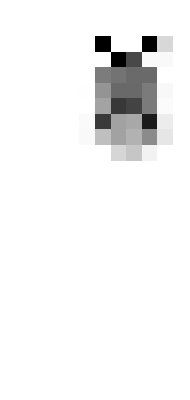

```mathematica
ArrayPlot[RunCode20Interped[NonlinearSumInterpolation][gci[Values[Last[]]], 20]]
```

```mathematica
MinimalBy[RandomSample[Range[0, 2^numBits-1, 0.1], 1000], f]
```

{214.}

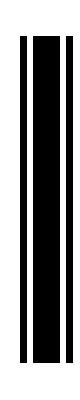

```mathematica
ArrayPlot[RunCode20Interped[LinearSumInterpolation][gci[#], 100]]&/@%
```